```mathematica
Show[Graphics3D[{Red,Opacity[0.5],Tetrahedron[{{1,1,0},{1,1,1},{0,2,1},{0,.5,0}}]},Boxed->False],
Graphics3D[Line[{{0,0,0},{2,0,0}}]],
Graphics3D[Line[{{0,0,0},{0,2,0}}]],
Graphics3D[Line[{{0,0,0},{0,0,2}}]],
Graphics3D[{PointSize->Large,Point[{{1,1,0},{1,1,1},{0,2,1},{0,.5,0}}]}]
]
```

```mathematica
triangle={{.5,-0.6},{-0.4,0.6},{0.8,0.5}}
```

{{0.5,-0.6},{-0.4,0.6},{0.8,0.5}}

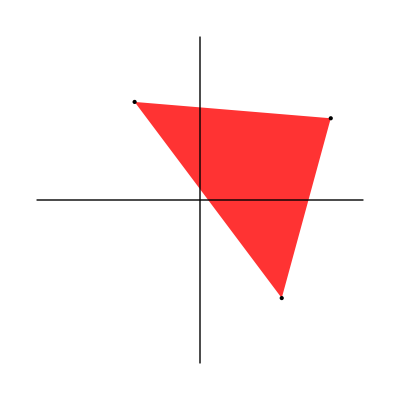

```mathematica
Show[
Graphics[{Red,Opacity[0.8],Triangle[triangle]}],Graphics[{PointSize->Large,Point[triangle]}],
Graphics[Line[{{-1,0},{1,0}}]],
Graphics[Line[{{0,-1},{0,1}}]]
]
```

```mathematica
Show[
Graphics[Line[{{-2,0},{2,0}}]],
Graphics[{Red,Line[{{-0.5,0},{1.6,0}}]}],
Graphics[{PointSize->Large,Point[{{-0.5,0},{1.6,0}}]}]
]
```

```mathematica
triangle2 ={{.5,-0.6},{-0.4,0.6},{-1.1,-0.3}};
```

```mathematica
triangle3 = {{1.1,-0.5},{1,-0.1},{1.4,-0.25}};
```

```mathematica
Show[
Graphics[{Red,Opacity[0.8],Triangle[triangle]}],Graphics[{PointSize->Large,Point[triangle]}],
Graphics[{Red,Opacity[0.8],Triangle[triangle2]}],Graphics[{PointSize->Large,Point[triangle2]}],
Graphics[{Red,Opacity[0.8],Triangle[triangle3]}],
Graphics[{PointSize->Large,Point[triangle3]}],
Table[Graphics[{Thick,Line[u]}],{u,Tuples[triangle2,2]}],
Table[Graphics[{Thick,Line[u]}],{u,Tuples[triangle,2]}],
Table[Graphics[{Thick,Line[u]}],{u,Tuples[triangle3,2]}],
Graphics[{Thick,Line[{{.5,-0.6},{1.1,-0.5}}]}],
Graphics[Line[{{-1.6,0},{1.5,0}}]],
Graphics[Line[{{0,-1},{0,1}}]]
]
```

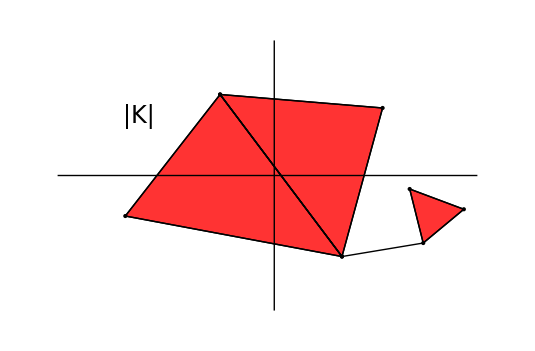

```mathematica
triangle4={{-0.4,-0.7},{-0.1,0.8},{0.6,0.9}};
```

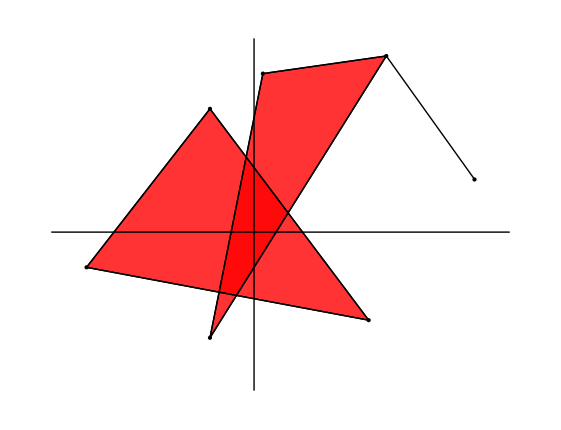

```mathematica
Show[
Graphics[{Red,Opacity[0.8],Triangle[triangle2]}],Graphics[{PointSize->Large,Point[triangle2]}],
Graphics[{Red,Opacity[0.8],Triangle[triangle4]}],
Graphics[{PointSize->Large,Point[triangle4]}],
Table[Graphics[{Thick,Line[u]}],{u,Tuples[triangle2,2]}],
Table[Graphics[{Thick,Line[u]}],{u,Tuples[triangle4,2]}],
Graphics[{Thick,Line[{{0.6,0.9},{1.1,0.2}}]}],
Graphics[{PointSize->Large,Point[{1.1,0.2}]}],
Graphics[Line[{{-1.3,-0.1},{1.3,-0.1}}]],
Graphics[Line[{{-0.15,-1},{-0.15,1}}]]
]
```

```mathematica
Show[
Graphics[{Thick,Red,Line[{{1,0},{0,1}}]}],
Graphics[{PointSize->Large,Point[{1,0}]}],
Graphics[{PointSize->Large,Point[{0,1}]}],
Graphics[Line[{{-0.3,0},{1.3,0}}]],
Graphics[Line[{{0,-0.3},{0,1.3}}]]
]
```

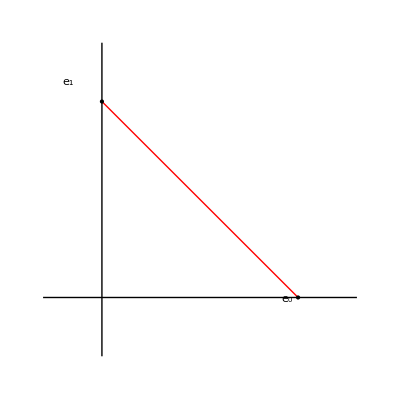

```mathematica
Show[
Graphics[Line[{{-0.2,0},{1.4,0}}]],
Graphics[{PointSize->Large,Red,Point[{{1,0}}]}]
]
```

```mathematica
Show[
Graphics3D[Line[{{0,0,0},{1.2,0,0}}],Boxed->False],
Graphics3D[Line[{{0,0,0},{0,1.2,0}}]],
Graphics3D[Line[{{0,0,0},{0,0,1.2}}]],
Graphics3D[{PointSize->Large,Point[{{1,0,0},{0,1,0},{0,0,1}}]}],
ContourPlot3D[x+y+z-1==0,{x,0,1},{y,0,1},{z,0,1},Axes->None,Mesh->None,ContourStyle->{Red,Opacity[0.8]},Boxed->False]
]
```

-Graphics3D-

```mathematica
standardbase3={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Show[
Graphics3D[Line[{{0,0,0},{1.2,0,0}}],Boxed->False],
Graphics3D[Line[{{0,0,0},{0,1.2,0}}]],
Graphics3D[Line[{{0,0,0},{0,0,1.2}}]],
Table[Graphics3D[{Thick,Red,Line[u],Boxed->False}],{u,Tuples[standardbase3,2]}],
Graphics3D[{PointSize->Large,Point[{{1,0,0},{0,1,0},{0,0,1}}]}]
]
```